Last modified on: Sunday, July 8, 2018 at 10:53

Author Info

Jaime Buitrago

Sebastian Bodenstein

Visible Impact Corporation

Poster Session Content

Authorship Identification by Using a Machine Learning Approach

Given sufficient amounts of text with the authors’ information tagged, can we accurately produce a feature vector that describes the style of the author and represents a fingerprint of its style?

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics3D-

Reuters 50/50 is a database of 5000 news articles written by 50 different authors.  It serves as a baseline for authorship identification.  Several classification methods were tried in order to evaluate their accuracy.  Wolfram’s Classify function was used on full articles, sentences and normalized sentences.  The output was further processed to improve accuracy.  These results were compared with an ad-hoc neural network classifier using two different pre-trained neural networks: Glove-100 and ELMo Contextual as feature extractors, and further processing their output with various combinations of LSTM and GRL layers.  The best results, 65% accuracy,  were obtained by using Wolfram’s Classifier on the full text articles, as well as using the same function on sentences and post-processing the result using a probabilistic model.  The best published results show a classification accuracy of 69.1%.

It will be necessary to work on the parameters of the neural networks in the model.  Extensive training with the ELMo Contextual neural network will be necessary to assess its contribution to accuracy improvement.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Project Workflow

-Graphics-

Classification Results

-Graphics--Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

Reuters 50/50 is a database of 5000 news articles written by 50 different authors.  It serves as a baseline for authorship identification.  Several classification methods were tried in order to evaluate their accuracy.  Wolfram’s Classify function was used on full articles, sentences and normalized sentences.  The output was further processed to improve accuracy.  These results were compared with an ad-hoc neural network classifier using two different pre-trained neural networks: Glove-100 and ELMo Contextual as feature extractors, and further processing their output with various combinations of LSTM and GRL layers.  The best results, 65% accuracy,  were obtained by using Wolfram’s Classifier on the full text articles, as well as using the same function on sentences and post-processing the result using a probabilistic model.  The best published results show a classification accuracy of 69.1%.

#### Code

Provide one of:

Link to the GitHub

Explicit code

#### Written Content / Lesson Plans

#### Conclusions in Detail

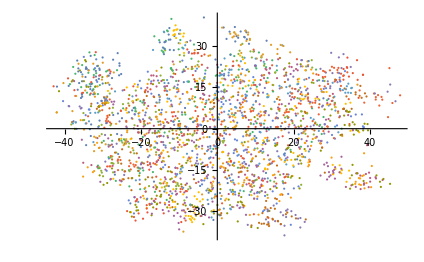
#### All Visualizations -Graphics3D--Graphics-

```mathematica
GraphicsRow[{-Graphics3D-,-Graphics3D-}]
```

-Graphics-

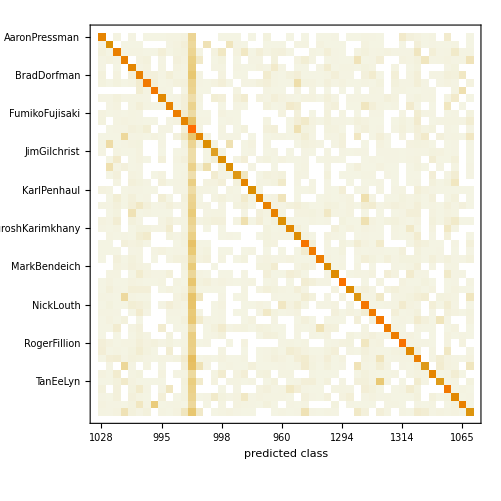

#### Data Sources Links/References

Trained neural networks were obtained from https://resources.wolframcloud.com/NeuralNetRepository/
Data was obtained from https://archive.ics.uci.edu/ml/machine-learning-databases/00217/C50.zip

#### Future Directions

It will be necessary to work on the parameters of the neural networks in the model.  Extensive training with the ELMo Contextual neural network will be necessary to assess its contribution to accuracy improvement.

#### Background Info Links/References

Chen Qian, Tianchang He,  Rao Zhang, Deep Learning based Autorship Identification, https://web.stanford.edu/class/cs224n/reports/2760185.pdf

#### Keywords

Provide keywords as items

authorship identification

deep learning

classify

#### Other information